```mathematica
(* a = 1/2 *)
mat = {{2^(1/2) u1, 2^(1/2) u2}, {u2, u1 - Pi^2}};
mat //MatrixForm
```

(√2 u1 | √2 u2
u2 | -π^2+u1)

```mathematica
eigs = Eigenvalues[mat]//Simplify
```

{1/2 (-π^2+u1+√2 u1-√(π^4+2 (-1+√2) π^2 u1+(3-2 √2) u1^2+4 √2 u2^2)),1/2 (-π^2+u1+√2 u1+√(π^4+2 (-1+√2) π^2 u1+(3-2 √2) u1^2+4 √2 u2^2))}

```mathematica
Solve[eigs[[2]]==0, u1]//Flatten//Simplify
foldline = First[Solve[eigs[[2]]==0, u1]]//Flatten//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{u1→1/2 (π^2-√(π^4+4 u2^2)),u1→1/2 (π^2+√(π^4+4 u2^2))}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{u1→1/2 (π^2-√(π^4+4 u2^2))}

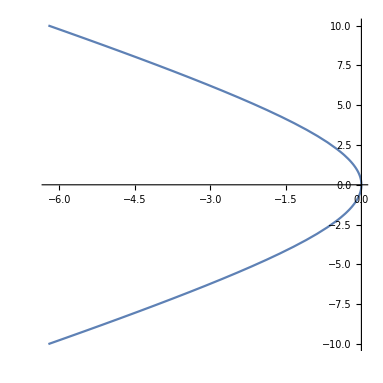

-Graphics-

```mathematica
ParametricPlot[{u1,u2} /. foldline,{u2, -10, 10},AspectRatio->1]
```

```mathematica
critmanif[u1_, u2_] :={{2^(1/2)u1^2+ 2^(1/2)u2^2},{-Pi^2/4 u2+u1 u2}};
{v1line, v2line} =critmanif[u1, u2]/.foldline//Flatten//Simplify
Plot[{v1line, v2line}, {u2, -10, 10}, PlotLabels->Automatic, AxesLabel->Automatic]
```

{(π^4+4 u2^2-π^2 √(π^4+4 u2^2))/(√2),1/4 u2 (π^2-2 √(π^4+4 u2^2))}

-Graphics-

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{u2→-1/2 √(-π^4/2+√2 v1-1/2 π^2 √(π^4+4 √2 v1))},{u2→1/2 √(-π^4/2+√2 v1-1/2 π^2 √(π^4+4 √2 v1))},{u2→-(√(-π^4+2 √2 v1+π^2 √(π^4+4 √2 v1)))/(2 √2)},{u2→(√(-π^4+2 √2 v1+π^2 √(π^4+4 √2 v1)))/(2 √2)}}

{(√(-π^4+2 √2 v1+π^2 √(π^4+4 √2 v1)) (-π^2+√2 √(π^4+2 √2 v1+π^2 √(π^4+4 √2 v1))))/(8 √2),(√(-π^4+2 √2 v1+π^2 √(π^4+4 √2 v1)) (π^2-√2 √(π^4+2 √2 v1+π^2 √(π^4+4 √2 v1))))/(8 √2)}

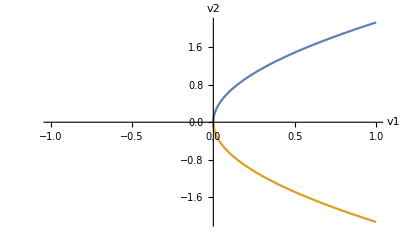

```mathematica
v1sols =Solve[v1line ==v1, u2]//Simplify
(*Solve[v2line ==v2, u2]//Simplify*)
{expr1, expr2}={v2line/.v1sols[[3]],v2line/.v1sols[[4]]}//Simplify
Plot[{v2line/.v1sols[[3]],v2line/.v1sols[[4]]}, {v1, -1, 1}, AxesLabel->{v1, v2}]
```

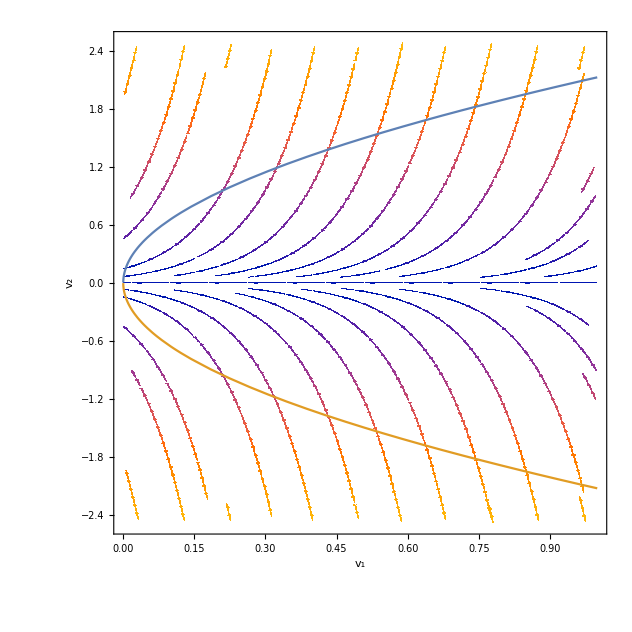

```mathematica
Show[StreamPlot[{-1,-9 v2},{v1, 0, 1}, {v2, -2.5, 2.5},StreamMarkers->"PinDart",StreamPoints->Fine], Plot[{v2line/.v1sols[[3]],v2line/.v1sols[[4]]}, {v1, -1, 1}],FrameLabel->{Subscript[v, 1],Subscript[v, 2]}]
```

```mathematica
mat3d = {{2^(1/2)u1, 2^(1/2)u2, 2^(1/2)u3}, {2^(1/2)u2, 1/4b2+2^(1/2)u1+u3, u2}, {2^(1/2)u3, u2, 1/4 b3+2^(1/2)u1}}/. {b2->-Pi^2, b3->-4 Pi^2};
mat3d //MatrixForm
```

(√2 u1 | √2 u2 | √2 u3
√2 u2 | -π^2/4+√2 u1+u3 | u2
√2 u3 | u2 | -π^2+√2 u1)

```mathematica
mat3d // Eigenvalues //Simplify
```

{1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,1],1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,2],1/4 Root[-16 √2 π^4 u1+160 π^2 u1^2-128 √2 u1^3-128 π^2 u2^2+192 √2 u1 u2^2+64 √2 π^2 u1 u3-128 u1^2 u3-256 u2^2 u3-32 π^2 u3^2+128 √2 u1 u3^2+128 u3^3+(4 π^4-40 √2 π^2 u1+96 u1^2-48 u2^2-16 π^2 u3+32 √2 u1 u3-32 u3^2) #1+(5 π^2-12 √2 u1-4 u3) #1^2+#1^3&,3]}

```mathematica
- Collect[CharacteristicPolynomial[mat3d,x],x]
```

-(π^4 u1)/(2 √2)+(5 π^2 u1^2)/2-2 √2 u1^3-2 π^2 u2^2+3 √2 u1 u2^2+√2 π^2 u1 u3-2 u1^2 u3-4 u2^2 u3-(π^2 u3^2)/2+2 √2 u1 u3^2+2 u3^3-(-π^4/4+(5 π^2 u1)/(√2)-6 u1^2+3 u2^2+π^2 u3-2 √2 u1 u3+2 u3^2) x-(-(5 π^2)/4+3 √2 u1+u3) x^2+x^3

```mathematica
b=-(-(5 π^2)/4+3 √2 u1+u3);
c=-(-π^4/4+(5 π^2 u1)/(√2)-6 u1^2+3 u2^2+π^2 u3-2 √2 u1 u3+2 u3^2) ;
d=-(π^4 u1)/(2 √2)+(5 π^2 u1^2)/2-2 √2 u1^3-2 π^2 u2^2+3 √2 u1 u2^2+√2 π^2 u1 u3-2 u1^2 u3-4 u2^2 u3-(π^2 u3^2)/2+2 √2 u1 u3^2+2 u3^3;
RegionPlot3D[{d>0 ,b c > d},{u1, -3, 1}, {u2, -5, 5}, {u3, -5, 5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[{b==0,d==0 ,b c == d},{u1, -3, 0}, {u2, -5, 5}, {u3, -5, 5},AxesLabel->Automatic, Mesh->None,ContourStyle->Opacity[0.8]],ParametricPlot3D[{u1, 0, 0},{u1, -3, 0},PlotStyle->{Red,Thick} ]]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[d==0,{u1, -3, 0}, {u2, -5, 5}, {u3, -5, 5},AxesLabel->{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]}, Mesh->None,ContourStyle->Opacity[0.8]],ParametricPlot3D[{u1, 0, 0},{u1, -3, 0},PlotStyle->{Red,Thick} ]]
```

-Graphics3D-

```mathematica
b c - d/.{u2->0, u3->0, u1->-0.01}//Simplify
b/.{u2->0, u3->0, u1->-0.01}//Simplify
d/.{u2->0, u3->0, u1->-0.01}//Simplify
```

305.448

12.3794

0.346863